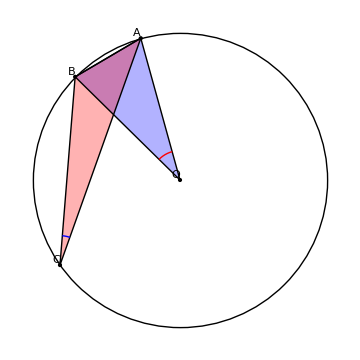

```mathematica
(* PIANO B con GRAPHICS*)
circleCenter = {0,0};

(* 1. generare angoli alla circonferenza partendo da angolo al centro*)

(*ampiezza angolo al centro*)
input =0;
(*Slider[Dynamic[input]]*)
alpha =  ((Mod[input , 180]/. input -> 30)/.value_/; value == 0 -> 180)°;
AAngle = RandomReal[{0, Pi}]; 
circAngle = RandomReal[{alpha + 0.1, 2*Pi - 0.1 }];

(*a = CirclePoints[{1, AAngle}, 1][[1]];
b = RotationMatrix[alpha].a;
c = RotationMatrix[circAngle].a; *)

points = {CirclePoints[{1, AAngle}, 1][[1]]};
AppendTo[points,  RotationMatrix[alpha].points[[1]]];
AppendTo[points,  RotationMatrix[circAngle].points[[1]]];

Graphics[{
Circle[circleCenter, 1] ,
Point[circleCenter],
Point /@ points,

{Opacity[0.3],Style[Triangle[{points[[1]],points[[2]],circleCenter}], Blue]},
{Opacity[0.3],Style[Triangle[points], Red]},

Line[Append[points,  points[[1]]]],(* triangolo con angolo al centro *)
Line[{points[[1]],points[[2]],circleCenter, points[[1]]}], (* triangolo con angolo alla circonferenza *)

Tooltip[Style[Circle[circleCenter, 0.2, {AAngle, AAngle + alpha}], Red, Thick ], alpha],
Tooltip[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2],
(* Annotation[Style[Circle[points[[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2, "Mouse"], *)

MapIndexed[ Text[FromCharacterCode[#2[[1]]+ 64] , #1, {1.5,-1.5}]&, points], 
Text["O", circleCenter,{1.5,-1.5}]
}, ImageSize -> Medium]/.{angletemp -> PlanarAngle[points[[3]] -> { {points[[3]][[1]] + 1, points[[3]][[2]]}, points[[1]]}]}

(*Angolo : Dynamic[MouseAnnotation[]] *)
(*Dynamic[input]*)
```